```mathematica
sampleDensity = 10;(*sample density of the trjectory record*)
traceSET=4;
gSET=10;
hSET=7;


yLst={0,0,0,0,1,1,1,1};
mLst={0,1,0,1,0,1,0,1};
aLst={0,0,1,1,0,0,1,1};
fH[gg_,hh_,ii_]:=Exp[-hh*((x1-1/2)*(mLst[[ii]]-1/2)+(x2-1/2)*(aLst[[ii]]-1/2))+gg/2*(yLst[[ii]]-mLst[[ii]]*aLst[[ii]])^2];
matJumpLST=Transpose[({{-(fH[g,h,1]*3), fH[g,h,1], fH[g,h,1], 0, fH[g,h,1], 0, 0, 0}, {fH[g,h,2], -(fH[g,h,2]*3), 0, fH[g,h,2], 0, fH[g,h,2], 0, 0}, {fH[g,h,3], 0, -(fH[g,h,3]*3), fH[g,h,3], 0, 0, fH[g,h,3], 0}, {0, fH[g,h,4], fH[g,h,4], -(fH[g,h,4]*3), 0, 0, 0, fH[g,h,4]}, {fH[g,h,5], 0, 0, 0, -(fH[g,h,5]*3), fH[g,h,5], fH[g,h,5], 0}, {0, fH[g,h,6], 0, 0, fH[g,h,6], -(fH[g,h,6]*3), 0, fH[g,h,6]}, {0, 0, fH[g,h,7], 0, fH[g,h,7], 0, -(fH[g,h,7]*3), fH[g,h,7]}, {0, 0, 0, fH[g,h,8], 0, fH[g,h,8], fH[g,h,8], -(fH[g,h,8]*3)}})];(*NEQ matrix, EQ matrix*)

timeLST={1,2,3,4,5,6};
signalLST={4,4,4,1,4,1,1,4,4,4,1,1,1,4,4,4,1,1,4};
periods=Length[signalLST];


trajectoryLST=Table[0,{i,1,sampleDensity*periods}];


(*Propogator*)
fProp[j_,i_,t_,t0_]:=Sum[Exp[eigenVa[[m]]*(t-t0)]*eigenVeR[[m,j]]*eigenVeL[[m,i]],{m,1,8}];
(*Initialize*)
distT={1,0,0,0,0,0,0,0};
```

```mathematica
i=1;

While[i<=periods,
matJump=N[matJumpLST/.{g->gSET,h->hSET,x1->mLst[[signalLST[[i]]]],x2->aLst[[signalLST[[i]]]]}];
eigenVa=Eigenvalues[matJump];(*Transpose[eigenVeL].eigenVeR*) (*verify the orthogonality of left- and right-eigenvectors*)
eigenVeR=Eigenvectors[matJump];
eigenVeL=Eigenvectors[Transpose[matJump]];
eigenVeL=Table[eigenVeL[[i]]/(eigenVeL[[i]].eigenVeR[[i]]),{i,1,8}];Print[distT];
trajectoryLST[[(i-1)*sampleDensity+1;;i*sampleDensity]]=Table[Sum[(fProp[traceSET,k,t/sampleDensity,0]+fProp[traceSET-3,k,t/sampleDensity,0]+fProp[traceSET-2,k,t/sampleDensity,0]+fProp[traceSET-1,k,t/sampleDensity,0])*distT[[k]],{k,1,8}],{t,1,sampleDensity}];
distTR=Table[Sum[fProp[j,k,1,0]*distT[[k]],{k,1,8}],{j,1,8}];
distT=distTR;i++]
```

{1,0,0,0,0,0,0,0}

General::munfl: Exp[-1485.66] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.00517797,0.188949,0.188949,0.0310566,0.0000269937,0.00076312,0.00076312,0.584314}

{0.00263021,0.0942814,0.0942814,0.0164751,0.0000144784,0.000425724,0.000425724,0.791466}

{0.00158344,0.0553868,0.0553868,0.0104842,9.33644×10^-6,0.000287103,0.000287103,0.876575}

{0.697223,0.138363,0.138363,0.000027263,0.0206391,0.000801518,0.000801518,0.00378135}

{0.00527943,0.192719,0.192719,0.0316373,0.0000274921,0.000776556,0.000776556,0.576065}

{0.688939,0.142189,0.142189,0.0000280095,0.0211284,0.000822626,0.000822626,0.00388262}

{0.867389,0.0598788,0.0598788,0.0000119274,0.0104165,0.00036583,0.00036583,0.00169393}

{0.00521981,0.190503,0.190503,0.031296,0.0000271992,0.00076866,0.00076866,0.580913}

{0.00264739,0.0949201,0.0949201,0.0165734,0.0000145628,0.000428,0.000428,0.790068}

{0.0015905,0.0556492,0.0556492,0.0105246,9.37113×10^-6,0.000288038,0.000288038,0.876001}

{0.697208,0.13837,0.13837,0.0000272645,0.02064,0.000801559,0.000801559,0.00378155}

{0.869684,0.0588199,0.0588199,0.0000117205,0.0102788,0.000359956,0.000359956,0.00166578}

{0.917545,0.0367424,0.0367424,7.40724×10^-6,0.00740865,0.000237476,0.000237476,0.00107888}

{0.00520222,0.18985,0.18985,0.0311954,0.0000271129,0.000766331,0.000766331,0.582343}

{0.00264017,0.0946516,0.0946516,0.0165321,0.0000145274,0.000427043,0.000427043,0.790656}

{0.00158754,0.0555389,0.0555389,0.0105076,9.35654×10^-6,0.000287645,0.000287645,0.876242}

{0.697214,0.138367,0.138367,0.0000272639,0.0206396,0.000801542,0.000801542,0.00378147}

{0.869686,0.058819,0.058819,0.0000117203,0.0102787,0.000359951,0.000359951,0.00166576}

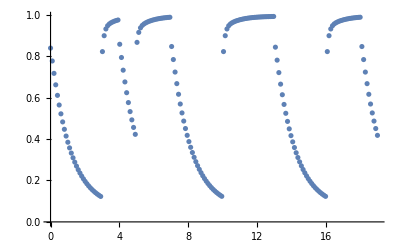

```mathematica
ListPlot[trajectoryLST,DataRange->{0,periods}]
```